My growing list of utility functions I keep copy and pasting everywhere

```mathematica
xyrtoabbc[{x_,y_,r_}]:={r(x^2/r^2+y^2/r^2-1),1/r,x/r,y/r}
graphFromG[G_]:=PlanarGraph[AdjacencyGraph[If[#==-1,1,0]&/@#&/@G,VertexLabels->"Name"]]
abbctoxyr[{bt_,b_,h1_,h2_}]:={h1/b,h2/b,1/b}
graphDuals[circs_]:=Graphics[{Red,Dashed,Circle[{#⟦1⟧,#⟦2⟧},Abs[#⟦3⟧]]&/@circs}]
graphCircles[circs_]:=Graphics[Circle[{#⟦1⟧,#⟦2⟧},Abs[#⟦3⟧]]&/@circs]
graphAbbc[circs_]:=graphCircles[abbctoxyr/@circs]
graphDualAbbc[circs_]:=graphDuals[abbctoxyr/@circs]
findRoot[tuple_,sigmas_]:=Block[{candidates},
candidates=Select[sigmas,Total[#.tuple]<Total[tuple]&];
If[Length[candidates]==0,tuple,findRoot[candidates⟦1⟧.tuple,sigmas]]]
reflectx:={{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, 1}}
reflecty:={{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, -1}}
scale[a_]:={{a, 0, 0, 0}, {0, 1/a, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}}
rotate[θ_]:={{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, Cos[θ], Sin[θ]}, {0, 0, -Sin[θ], Cos[θ]}}
translate[s_,t_]:={{1, s^2+t^2, 2s, 2t}, {0, 1, 0, 0}, {0, s, 1, 0}, {0, t, 0, 1}}
invert:={{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}}
invertAboutCircle[{x_,y_,r_}]:=translate[x,y].scale[r].{{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}}.scale[1/r].translate[-x,-y]
invertAboutAbbc[{bt_,b_,h1_,h2_}]:=invertAboutCircle[abbctoxyr[{bt,b,h1,h2}]]
```

```mathematica
gextFromG[G_]:=Block[{a,b,d,faces,nl,m},
nl=Length[G];
faces=FindFace[graphFromG[G]];
m=Length[faces];
a=G;
b=Table[With[{n=faces[[j,1]],x=i,one=faces[[j,2]],two=faces[[j,3]]},√(1-G[[n,x]]^2-(G[[one,x]]+G[[n,x]])/(1-G[[two,n]])(G[[two,n]]G[[n,x]]-G[[two,n]]G[[one,x]]-G[[one,x]]-G[[n,x]]-2G[[two,x]]))],{i,nl},{j,m}];
d=bᵀ.PseudoInverse[a].b;
ArrayFlatten[{{a, b}, {bᵀ, d}}]
]
```

Function to find root tuple just given G. It needs to know three rows of G corresponding to three circles on a face. It defaults to {1, 2, 3}, but you can change that with Face->whatever. Likewise, it will default to inverting through circle 4 to make the bounded packing, but you can change that with Invert->whatever. I’d recommend not picking anything on the face, since two of them don’t work as they are lines and the other can often give extra unwanted symmetry. Finally, it defaults to doing everything numerically, but you can make it exact by specifying Exact->True.

```mathematica
Options[rootTupleFromG]={"Face"->{1,2,3},"Invert"->4,"Exact"->False};
rootTupleFromG[G_,OptionsPattern[]]:=Block[{circs,P,v,c1,c2,c3,face,invert,exact},
P={{0, -1/2, 0, 0}, {-1/2, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}};
face=OptionValue["Face"];
invert=OptionValue["Invert"];
exact=OptionValue["Exact"];
v={bt,b,h1,h2};
c1=face[[1]];
c2=face[[2]];
c3=face[[3]];
circs=Range[Length[G]];
circs[[c1]]={2,0,0,1};
circs[[c2]]={0,0,0,-1};
circs[[c3]]={(1-G[[c2,c3]]^2)/(G[[c1,c3]]+G[[c2,c3]]),-G[[c1,c3]]-G[[c2,c3]],0,-G[[c2,c3]]};
For[i=1,i<=Length[G],i++,
If[Not[MemberQ[i,face]],
circs[[i]]=v/.(If[exact,Solve,NSolve][circs[[c1]].P.v==G[[c1,i]]&&circs[[c2]].P.v==G[[c2,i]]&&circs[[c3]].P.v==G[[c3,i]]&&h1^2+h2^2-b bt==1,{bt,b,h1,h2}][[1]]);
]
];
invertAboutAbbc[circs[[invert]]].#&/@circs
]
```

```mathematica
icos={{1,-1,-4-Sqrt[5],-1,-2-Sqrt[5],-1,-2-Sqrt[5],-2-Sqrt[5],-1,-1,-2-Sqrt[5],-2-Sqrt[5]},{-1,1,-2-Sqrt[5],-2-Sqrt[5],-1,-1,-4-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-1,-2-Sqrt[5],-1},{-4-Sqrt[5],-2-Sqrt[5],1,-2-Sqrt[5],-1,-2-Sqrt[5],-1,-1,-2-Sqrt[5],-2-Sqrt[5],-1,-1},{-1,-2-Sqrt[5],-2-Sqrt[5],1,-4-Sqrt[5],-2-Sqrt[5],-1,-1,-1,-1,-2-Sqrt[5],-2-Sqrt[5]},{-2-Sqrt[5],-1,-1,-4-Sqrt[5],1,-1,-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-1,-1},{-1,-1,-2-Sqrt[5],-2-Sqrt[5],-1,1,-2-Sqrt[5],-4-Sqrt[5],-1,-2-Sqrt[5],-1,-2-Sqrt[5]},{-2-Sqrt[5],-4-Sqrt[5],-1,-1,-2-Sqrt[5],-2-Sqrt[5],1,-1,-1,-2-Sqrt[5],-1,-2-Sqrt[5]},{-2-Sqrt[5],-2-Sqrt[5],-1,-1,-2-Sqrt[5],-4-Sqrt[5],-1,1,-2-Sqrt[5],-1,-2-Sqrt[5],-1},{-1,-2-Sqrt[5],-2-Sqrt[5],-1,-2-Sqrt[5],-1,-1,-2-Sqrt[5],1,-2-Sqrt[5],-1,-4-Sqrt[5]},{-1,-1,-2-Sqrt[5],-1,-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-1,-2-Sqrt[5],1,-4-Sqrt[5],-1},{-2-Sqrt[5],-2-Sqrt[5],-1,-2-Sqrt[5],-1,-1,-1,-2-Sqrt[5],-1,-4-Sqrt[5],1,-2-Sqrt[5]},{-2-Sqrt[5],-1,-1,-2-Sqrt[5],-1,-2-Sqrt[5],-2-Sqrt[5],-1,-4-Sqrt[5],-1,-2-Sqrt[5],1}};
```

```mathematica
root=rootTupleFromG[icos,"Invert"->3,"Face"->{1,2,10},"Exact"->True]//FullSimplify
```

{{6 (9+4 √5),68+28 √5,-4 (13+6 √5),3 (9+4 √5)},{4 (9+4 √5),44+20 √5,-4 (9+4 √5),17+8 √5},{-2 (2+√5),-2 (3+√5),2 (2+√5),-2-√5},{39+17 √5,47+21 √5,-37-17 √5,20+9 √5},{11+5 √5,5 (3+√5),-11-5 √5,5+2 √5},{39+17 √5,46+20 √5,-37-17 √5,19+8 √5},{14+6 √5,6 (3+√5),-6 (2+√5),8+3 √5},{11+5 √5,16+6 √5,-11-5 √5,3 (2+√5)},{40+18 √5,47+21 √5,-39-17 √5,20+9 √5},{4 (9+4 √5),46+20 √5,-4 (9+4 √5),19+8 √5},{14+6 √5,16+6 √5,-6 (2+√5),3 (2+√5)},{10+4 √5,5 (3+√5),-9-5 √5,5+2 √5}}

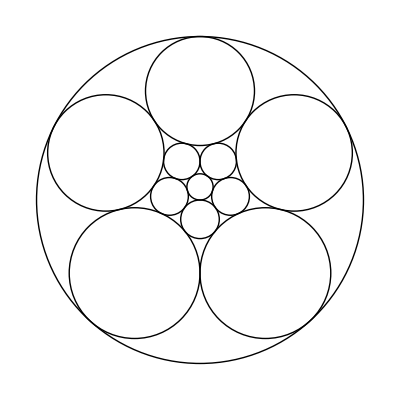

```mathematica
graphAbbc[root]
```

```mathematica
cube
```

{{1,-1,-3,-1,-1,-3,-5,-3},{-1,1,-1,-3,-3,-1,-3,-5},{-3,-1,1,-1,-5,-3,-1,-3},{-1,-3,-1,1,-3,-5,-3,-1},{-1,-3,-5,-3,1,-1,-3,-1},{-3,-1,-3,-5,-1,1,-1,-3},{-5,-3,-1,-3,-3,-1,1,-1},{-3,-5,-3,-1,-1,-3,-1,1}}

```mathematica
gextFromG[squareTriangle]//Chop//MatrixForm
```

(1 | -11.0876 | -1 | -3.65722 | -8.77328 | -10.0385 | -3. | -3.54536 | -3.02001 | -3.53849 | -6.7126 | -7.56229 | -9.67176 | -1 | -1 | -1 | -6.7691 | -7.67176 | -6.11607 | -7.85703 | 0 | 0 | 0 | 0 | 6.36131 | 6.71744 | 6.05593 | 3.01572 | 2. | 2.83751 | 4.36131 | 2.65277 | 4.06022
-11.0876 | 1 | -7.85703 | -9.26401 | -1 | -1 | -10.4879 | -9.399 | -9.58535 | -9.50103 | -4.28293 | -4.30294 | -1 | -18.3547 | -12.5144 | -13.7185 | -4.28261 | -4.23061 | -4.25042 | -4.21842 | 20.8767 | 8.56554 | 8.07023 | 10.6319 | 0 | 0 | 0 | 3.19893 | 5.33493 | 5.19873 | 3.23061 | 5.42167 | 3.25042
-1 | -7.85703 | 1 | -8.77328 | -3.65722 | -10.0385 | -1 | -6.7126 | -3.02001 | -6.7691 | -3.54536 | -7.56229 | -7.67176 | -1 | -6.11607 | -3. | -3.53849 | -9.67176 | -1 | -11.0876 | 0 | 2. | 3.01572 | 9.65706×10^-8 | 4.36131 | 6.71744 | 2.83751 | 0 | 0 | 6.05593 | 6.36131 | 2.65277 | 4.06022
-3.65722 | -9.26401 | -8.77328 | 1 | -12.0871 | -4.16724 | -9.77545 | -1 | -9.44986 | -4.25042 | -9.10191 | -4.23061 | -9.31499 | -14.0296 | -1 | -4.65939 | -12.5144 | -4.19893 | -14.0871 | -1 | 14.4042 | 3.28261 | 0 | 6.27013 | 5.11607 | 3.19893 | 8.23283 | 7.7143 | 8.39868 | 0 | 0 | 3.30294 | 5.19893
-8.77328 | -1 | -3.65722 | -12.0871 | 1 | -4.16724 | -4.65939 | -9.10191 | -9.44986 | -12.5144 | -1 | -4.23061 | -4.19893 | -14.0296 | -14.0871 | -9.77545 | -4.25042 | -9.31499 | -1 | -9.26401 | 14.4042 | 8.39868 | 7.7143 | 6.27013 | 0 | 3.19893 | 0.+1.4484×10^-7 ⅈ | 1.03238×10^-7 | 3.28261 | 8.23283 | 5.11607 | 3.30294 | 5.19893
-10.0385 | -1 | -10.0385 | -4.16724 | -4.16724 | 1 | -10.1063 | -4.19893 | -12.953 | -9.58535 | -4.19893 | -1 | -4.25042 | -21.902 | -9.44986 | -10.1063 | -9.58535 | -4.25042 | -9.44986 | -1 | 23.2702 | 8.67039 | 5.06589 | 10.1219 | 0.+1.44393×10^-7 ⅈ | 0 | 3.23061 | 5.06589 | 8.67039 | 3.23061 | 0 | 3.28293 | 5.28261
-3. | -10.4879 | -1 | -9.77545 | -4.65939 | -10.1063 | 1 | -4.16724 | -11.6917 | -14.6941 | -1 | -4.42688 | -14.4849 | -10.0648 | -10.3757 | -1 | -11.4635 | -16.4849 | -5.25963 | -13.7185 | 6.65277 | 6.41206 | 3.01572 | 0 | 3.42688 | 9.32254 | 6.04337 | 0 | 4.41206 | 9.26179 | 5.42688 | 0 | 9.92278
-3.54536 | -9.399 | -6.7126 | -1 | -9.10191 | -4.19893 | -4.16724 | 1 | -13.2352 | -9.843 | -4.01572 | -1 | -12.7862 | -15.7039 | -4.42114 | -1 | -14.9591 | -9.61891 | -12.5231 | -4.28293 | 13.6341 | 5.61514 | 2.02129×10^-7 | 3.42688 | 3.16724 | 5.25093 | 8.39971 | 4.77576 | 8.78238 | 3.30294 | 1.04388×10^-7 | 0.+5.96046×10^-8 ⅈ | 8.67207
-3.02001 | -9.58535 | -3.02001 | -9.44986 | -9.44986 | -12.953 | -11.6917 | -13.2352 | 1 | -1 | -13.2352 | -15.5113 | -4.25042 | -1 | -4.16724 | -11.6917 | -1 | -4.25042 | -4.16724 | -9.58535 | 4.02001 | 0 | 5.06589 | 6.0257 | 8.67039 | 5.28261 | 3.23061 | 5.06589 | 1.3328×10^-7 | 3.23061 | 8.67039 | 9.482 | 0
-3.53849 | -9.50103 | -6.7691 | -4.25042 | -12.5144 | -9.58535 | -14.6941 | -9.843 | -1 | 1 | -14.9591 | -13.2318 | -4.23061 | -5.49354 | -1 | -11.4635 | -4.21842 | -1 | -9.26401 | -4.28261 | 9.03203 | 0.+4.21468×10^-8 ⅈ | 3.19893 | 8.11147 | 8.56554 | 3.25042 | 5.19873 | 8.07023 | 3.23061 | 0.+5.96046×10^-8 ⅈ | 5.33493 | 9.23599 | 0.+1.26055×10^-7 ⅈ
-6.7126 | -4.28293 | -3.54536 | -9.10191 | -1 | -4.19893 | -1 | -4.01572 | -13.2352 | -14.9591 | 1 | -1 | -9.61891 | -15.7039 | -12.5231 | -4.16724 | -9.843 | -12.7862 | -4.42114 | -9.399 | 13.6341 | 8.78238 | 4.77576 | 3.42688 | 0 | 5.25093 | 3.30294 | 0 | 5.61514 | 8.39971 | 3.16724 | 1.19209×10^-7 | 8.67207
-7.56229 | -4.30294 | -7.56229 | -4.23061 | -4.23061 | -1 | -4.42688 | -1 | -15.5113 | -13.2318 | -1 | 1 | -9.70343 | -20.7384 | -9.7246 | -4.42688 | -13.2318 | -9.70343 | -9.7246 | -4.30294 | 19.2833 | 9.01732 | 3.16724 | 5.87174 | 0 | 3.28293 | 5.33526 | 3.16724 | 9.01732 | 5.33526 | 0 | 8.42937×10^-8 | 8.77692
-9.67176 | -1 | -7.67176 | -9.31499 | -4.19893 | -4.25042 | -14.4849 | -12.7862 | -4.25042 | -4.23061 | -9.61891 | -9.70343 | 1 | -12.8363 | -9.31499 | -16.4849 | -1 | -1 | -4.19893 | -4.23061 | 17.2576 | 5.25042 | 8.13228 | 11.588 | 3.25042 | 0.+8.45517×10^-8 ⅈ | 0 | 5.11657 | 3.25042 | 3.21842 | 5.25042 | 8.95094 | 0
-1 | -18.3547 | -1 | -14.0296 | -14.0296 | -21.902 | -10.0648 | -15.7039 | -1 | -5.49354 | -15.7039 | -20.7384 | -12.8363 | 1 | -6.11607 | -10.0648 | -5.49354 | -12.8363 | -6.11607 | -18.3547 | 0 | 0 | 5.01572 | 3.32638 | 12.9885 | 11.9335 | 7.25844 | 5.01572 | 2.47537×10^-7 | 7.25844 | 12.9885 | 10.0235 | 4.02001
-1 | -12.5144 | -6.11607 | -1 | -14.0871 | -9.44986 | -10.3757 | -4.42114 | -4.16724 | -1 | -12.5231 | -9.7246 | -9.31499 | -6.11607 | 1 | -5.25963 | -9.26401 | -4.19893 | -12.0871 | -4.25042 | 7.11607 | 9.71253×10^-8 | 0 | 4.71932 | 8.39868 | 5.19893 | 8.23283 | 7.7143 | 5.11607 | 0 | 3.28261 | 5.64991 | 3.19893
-1 | -13.7185 | -3. | -4.65939 | -9.77545 | -10.1063 | -1 | -1 | -11.6917 | -11.4635 | -4.16724 | -4.42688 | -16.4849 | -10.0648 | -5.25963 | 1 | -14.6941 | -14.4849 | -10.3757 | -10.4879 | 6.65277 | 4.41206 | 2.07306×10^-7 | 0 | 5.42688 | 9.32254 | 9.26179 | 3.01572 | 6.41206 | 6.04337 | 3.42688 | 0 | 9.92278
-6.7691 | -4.28261 | -3.53849 | -12.5144 | -4.25042 | -9.58535 | -11.4635 | -14.9591 | -1 | -4.21842 | -9.843 | -13.2318 | -1 | -5.49354 | -9.26401 | -14.6941 | 1 | -4.23061 | -1 | -9.50103 | 9.03203 | 3.23061 | 8.07023 | 8.11147 | 5.33493 | 3.25042 | 0 | 3.19893 | 0 | 5.19873 | 8.56554 | 9.23599 | 0
-7.67176 | -4.23061 | -9.67176 | -4.19893 | -9.31499 | -4.25042 | -16.4849 | -9.61891 | -4.25042 | -1 | -12.7862 | -9.70343 | -1 | -12.8363 | -4.19893 | -14.4849 | -4.23061 | 1 | -9.31499 | -1 | 17.2576 | 3.25042 | 5.11657 | 11.588 | 5.25042 | 1.03238×10^-7 | 3.21842 | 8.13228 | 5.25042 | 1.78814×10^-7 | 3.25042 | 8.95094 | 1.19209×10^-7
-6.11607 | -4.25042 | -1 | -14.0871 | -1 | -9.44986 | -5.25963 | -12.5231 | -4.16724 | -9.26401 | -4.42114 | -9.7246 | -4.19893 | -6.11607 | -12.0871 | -10.3757 | -1 | -9.31499 | 1 | -12.5144 | 7.11607 | 5.11607 | 7.7143 | 4.71932 | 3.28261 | 5.19893 | 8.42937×10^-8 | 1.56407×10^-7 | 0 | 8.23283 | 8.39868 | 5.64991 | 3.19893
-7.85703 | -4.21842 | -11.0876 | -1 | -9.26401 | -1 | -13.7185 | -4.28293 | -9.58535 | -4.28261 | -9.399 | -4.30294 | -4.23061 | -18.3547 | -4.25042 | -10.4879 | -9.50103 | -1 | -12.5144 | 1 | 20.8767 | 5.33493 | 3.19893 | 10.6319 | 3.23061 | 0 | 5.19873 | 8.07023 | 8.56554 | 1.93141×10^-7 | 0 | 5.42167 | 3.25042
0 | 20.8767 | 0 | 14.4042 | 14.4042 | 23.2702 | 6.65277 | 13.6341 | 4.02001 | 9.03203 | 13.6341 | 19.2833 | 17.2576 | 0 | 7.11607 | 6.65277 | 9.03203 | 17.2576 | 7.11607 | 20.8767 | 1. | -1.-4.12597×10^-9 ⅈ | -4.01572 | -1. | -12.962+1.89833×10^-8 ⅈ | -14.3683+3.78462×10^-9 ⅈ | -9.09594-1.74567×10^-9 ⅈ | -4.01572 | -1. | -9.09594-5.83501×10^-9 ⅈ | -12.962 | -7.82413-2.6158×10^-9 ⅈ | -7.08023-1.23401×10^-8 ⅈ
0 | 8.56554 | 2. | 3.28261 | 8.39868 | 8.67039 | 6.41206 | 5.61514 | 0 | 0.+4.21468×10^-8 ⅈ | 8.78238 | 9.01732 | 5.25042 | 0 | 9.71253×10^-8 | 4.41206 | 3.23061 | 3.25042 | 5.11607 | 5.33493 | -1.-4.12597×10^-9 ⅈ | 1.-8.83632×10^-9 ⅈ | -1.-2.07536×10^-9 ⅈ | -2.32638+3.05486×10^-10 ⅈ | -6.38777+7.77964×10^-9 ⅈ | -4.28261-2.75904×10^-9 ⅈ | -4.21842+7.38505×10^-9 ⅈ | -4.01572+2.23546×10^-9 ⅈ | -1.-1.55926×10^-9 ⅈ | -1.-1.09925×10^-8 ⅈ | -4.38777-1.01028×10^-9 ⅈ | -4.85209+8.15014×10^-10 ⅈ | -1.-1.75055×10^-8 ⅈ
0 | 8.07023 | 3.01572 | 0 | 7.7143 | 5.06589 | 3.01572 | 2.02129×10^-7 | 5.06589 | 3.19893 | 4.77576 | 3.16724 | 8.13228 | 5.01572 | 0 | 2.07306×10^-7 | 8.07023 | 5.11657 | 7.7143 | 3.19893 | -4.01572 | -1.-2.07536×10^-9 ⅈ | 1. | -1. | -4.01572-1.11975×10^-9 ⅈ | -4.11657+4.41339×10^-9 ⅈ | -5.85292+7.89866×10^-9 ⅈ | -3.54727 | -4.01572 | -1.-2.935×10^-9 ⅈ | -1. | -1.-6.34191×10^-9 ⅈ | -4.11657-6.20708×10^-9 ⅈ
0 | 10.6319 | 9.65706×10^-8 | 6.27013 | 6.27013 | 10.1219 | 0 | 3.42688 | 6.0257 | 8.11147 | 3.42688 | 5.87174 | 11.588 | 3.32638 | 4.71932 | 0 | 8.11147 | 11.588 | 4.71932 | 10.6319 | -1. | -2.32638+3.05486×10^-10 ⅈ | -1. | 1. | -4.87174+5.91597×10^-9 ⅈ | -7.97644+5.98073×10^-9 ⅈ | -5.69555-3.44813×10^-9 ⅈ | -1. | -2.32638 | -5.69555+4.32022×10^-10 ⅈ | -4.87174 | -1.-4.85951×10^-9 ⅈ | -6.42563+9.13661×10^-10 ⅈ
6.36131 | 0 | 4.36131 | 5.11607 | 0 | 0.+1.44393×10^-7 ⅈ | 3.42688 | 3.16724 | 8.67039 | 8.56554 | 0 | 0 | 3.25042 | 12.9885 | 8.39868 | 5.42688 | 5.33493 | 5.25042 | 3.28261 | 3.23061 | -12.962+1.89833×10^-8 ⅈ | -6.38777+7.77964×10^-9 ⅈ | -4.01572-1.11975×10^-9 ⅈ | -4.87174+5.91597×10^-9 ⅈ | 1.-3.053×10^-8 ⅈ | -1.-2.09156×10^-8 ⅈ | -1.-2.36867×10^-8 ⅈ | -1.-1.11975×10^-9 ⅈ | -4.38777+5.93101×10^-9 ⅈ | -4.21842-4.93758×10^-9 ⅈ | -1.-1.5265×10^-8 ⅈ | -1.-9.90234×10^-9 ⅈ | -4.28261+2.37175×10^-9 ⅈ
6.71744 | 0 | 6.71744 | 3.19893 | 3.19893 | 0 | 9.32254 | 5.25093 | 5.28261 | 3.25042 | 5.25093 | 3.28293 | 0.+8.45517×10^-8 ⅈ | 11.9335 | 5.19893 | 9.32254 | 3.25042 | 1.03238×10^-7 | 5.19893 | 0 | -14.3683+3.78462×10^-9 ⅈ | -4.28261-2.75904×10^-9 ⅈ | -4.11657+4.41339×10^-9 ⅈ | -7.97644+5.98073×10^-9 ⅈ | -1.-2.09156×10^-8 ⅈ | 1.-1.90023×10^-8 ⅈ | -1.-1.64168×10^-8 ⅈ | -4.11657-9.40412×10^-10 ⅈ | -4.28261-4.09447×10^-9 ⅈ | -1.-6.87538×10^-9 ⅈ | -1.-1.2937×10^-9 ⅈ | -4.38883+2.94809×10^-9 ⅈ | -1.-1.56695×10^-8 ⅈ
6.05593 | 0 | 2.83751 | 8.23283 | 0.+1.4484×10^-7 ⅈ | 3.23061 | 6.04337 | 8.39971 | 3.23061 | 5.19873 | 3.30294 | 5.33526 | 0 | 7.25844 | 8.23283 | 9.26179 | 0 | 3.21842 | 8.42937×10^-8 | 5.19873 | -9.09594-1.74567×10^-9 ⅈ | -4.21842+7.38505×10^-9 ⅈ | -5.85292+7.89866×10^-9 ⅈ | -5.69555-3.44813×10^-9 ⅈ | -1.-2.36867×10^-8 ⅈ | -1.-1.64168×10^-8 ⅈ | 1.-3.37007×10^-8 ⅈ | -1.-1.55617×10^-8 ⅈ | -1.-8.02998×10^-9 ⅈ | -4.17912+7.98372×10^-9 ⅈ | -4.21842-5.76087×10^-10 ⅈ | -4.45471-4.24364×10^-9 ⅈ | -1.-2.45222×10^-9 ⅈ
3.01572 | 3.19893 | 0 | 7.7143 | 1.03238×10^-7 | 5.06589 | 0 | 4.77576 | 5.06589 | 8.07023 | 0 | 3.16724 | 5.11657 | 5.01572 | 7.7143 | 3.01572 | 3.19893 | 8.13228 | 1.56407×10^-7 | 8.07023 | -4.01572 | -4.01572+2.23546×10^-9 ⅈ | -3.54727 | -1. | -1.-1.11975×10^-9 ⅈ | -4.11657-9.40412×10^-10 ⅈ | -1.-1.55617×10^-8 ⅈ | 1. | -1. | -5.85292+3.16142×10^-9 ⅈ | -4.01572 | -1.-3.6507×10^-10 ⅈ | -4.11657+6.68592×10^-9 ⅈ
2. | 5.33493 | 0 | 8.39868 | 3.28261 | 8.67039 | 4.41206 | 8.78238 | 1.3328×10^-7 | 3.23061 | 5.61514 | 9.01732 | 3.25042 | 2.47537×10^-7 | 5.11607 | 6.41206 | 0 | 5.25042 | 0 | 8.56554 | -1. | -1.-1.55926×10^-9 ⅈ | -4.01572 | -2.32638 | -4.38777+5.93101×10^-9 ⅈ | -4.28261-4.09447×10^-9 ⅈ | -1.-8.02998×10^-9 ⅈ | -1. | 1. | -4.21842-2.20513×10^-9 ⅈ | -6.38777 | -4.85209+2.88262×10^-9 ⅈ | -1.-4.6635×10^-9 ⅈ
2.83751 | 5.19873 | 6.05593 | 0 | 8.23283 | 3.23061 | 9.26179 | 3.30294 | 3.23061 | 0.+5.96046×10^-8 ⅈ | 8.39971 | 5.33526 | 3.21842 | 7.25844 | 0 | 6.04337 | 5.19873 | 1.78814×10^-7 | 8.23283 | 1.93141×10^-7 | -9.09594-5.83501×10^-9 ⅈ | -1.-1.09925×10^-8 ⅈ | -1.-2.935×10^-9 ⅈ | -5.69555+4.32022×10^-10 ⅈ | -4.21842-4.93758×10^-9 ⅈ | -1.-6.87538×10^-9 ⅈ | -4.17912+7.98372×10^-9 ⅈ | -5.85292+3.16142×10^-9 ⅈ | -4.21842-2.20513×10^-9 ⅈ | 1.-1.34188×10^-8 ⅈ | -1.-1.42875×10^-9 ⅈ | -4.45471-6.52698×10^-10 ⅈ | -1.-2.02585×10^-8 ⅈ
4.36131 | 3.23061 | 6.36131 | 0 | 5.11607 | 0 | 5.42688 | 1.04388×10^-7 | 8.67039 | 5.33493 | 3.16724 | 0 | 5.25042 | 12.9885 | 3.28261 | 3.42688 | 8.56554 | 3.25042 | 8.39868 | 0 | -12.962 | -4.38777-1.01028×10^-9 ⅈ | -1. | -4.87174 | -1.-1.5265×10^-8 ⅈ | -1.-1.2937×10^-9 ⅈ | -4.21842-5.76087×10^-10 ⅈ | -4.01572 | -6.38777 | -1.-1.42875×10^-9 ⅈ | 1. | -1.-6.45964×10^-9 ⅈ | -4.28261-3.02158×10^-9 ⅈ
2.65277 | 5.42167 | 2.65277 | 3.30294 | 3.30294 | 3.28293 | 0 | 0.+5.96046×10^-8 ⅈ | 9.482 | 9.23599 | 1.19209×10^-7 | 8.42937×10^-8 | 8.95094 | 10.0235 | 5.64991 | 0 | 9.23599 | 8.95094 | 5.64991 | 5.42167 | -7.82413-2.6158×10^-9 ⅈ | -4.85209+8.15014×10^-10 ⅈ | -1.-6.34191×10^-9 ⅈ | -1.-4.85951×10^-9 ⅈ | -1.-9.90234×10^-9 ⅈ | -4.38883+2.94809×10^-9 ⅈ | -4.45471-4.24364×10^-9 ⅈ | -1.-3.6507×10^-10 ⅈ | -4.85209+2.88262×10^-9 ⅈ | -4.45471-6.52698×10^-10 ⅈ | -1.-6.45964×10^-9 ⅈ | 1.-1.32177×10^-8 ⅈ | -6.7358+8.194×10^-9 ⅈ
4.06022 | 3.25042 | 4.06022 | 5.19893 | 5.19893 | 5.28261 | 9.92278 | 8.67207 | 0 | 0.+1.26055×10^-7 ⅈ | 8.67207 | 8.77692 | 0 | 4.02001 | 3.19893 | 9.92278 | 0 | 1.19209×10^-7 | 3.19893 | 3.25042 | -7.08023-1.23401×10^-8 ⅈ | -1.-1.75055×10^-8 ⅈ | -4.11657-6.20708×10^-9 ⅈ | -6.42563+9.13661×10^-10 ⅈ | -4.28261+2.37175×10^-9 ⅈ | -1.-1.56695×10^-8 ⅈ | -1.-2.45222×10^-9 ⅈ | -4.11657+6.68592×10^-9 ⅈ | -1.-4.6635×10^-9 ⅈ | -1.-2.02585×10^-8 ⅈ | -4.28261-3.02158×10^-9 ⅈ | -6.7358+8.194×10^-9 ⅈ | 1.-2.56704×10^-8 ⅈ)